# Power and Punishment Influence Negotiations Over Parental Care

Barbasch, TA*, Alonzo, SH, and Buston, PM
1.	Department of Biology and Marine Program, Boston University
2.	Department of Ecology and Evolutionary Biology, University of California Santa Cruz

Correspondence: Tina Barbasch, Boston University, Department of Biology and Marine Program, 5 Cummington Mall, Boston MA 02215

Email address:  tbarbasc@bu.edu

Figure 1 - Four types of punishment cost

Plot four types of punishment cost functions: concave up increasing, concave up decreasing, concave down decreasing, concave down increasing

```mathematica
Concupinc[u2c_]:=u2c^2
Concupdec[u2c_]:=(u2c-1)^2
Concdowndec[u2c_]:=-u2c^2+1
Concdowninc[u2c_]:=2(u2c)-(u2c)^2
```

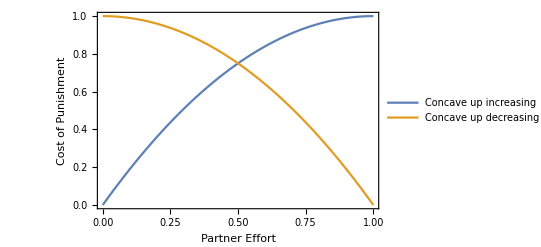

```mathematica
Plot[{Concdowninc[u2c],Concdowndec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},FrameLabel->{{"Cost of Punishment",None},{"Partner Effort",None}},PlotLegends->{"Concave up increasing","Concave up decreasing"},PlotStyle->{Default,Default}]
```

Generate four paneled figure

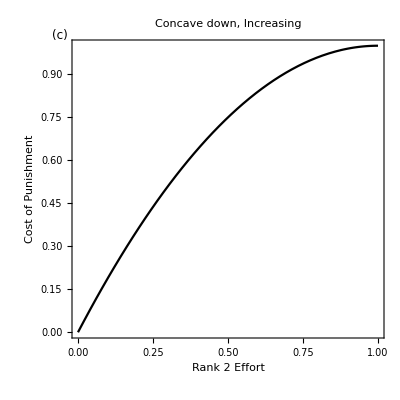

```mathematica
P1=Plot[{Concdowninc[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},FrameLabel->{Style["Rank 2 Effort",12,FontFamily->Arial,FontColor->Black],Style["Cost of Punishment",12,FontFamily->Arial,FontColor->Black]},PlotLabel->"Concave down, Increasing",Epilog->Text[Style["(c)",{Black,12}],Offset[{-20,5},Scaled[{0,1}]],{-1,0}],PlotRangeClipping->False,BaseStyle->{FontFamily->Arial,FontSize->8},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
```

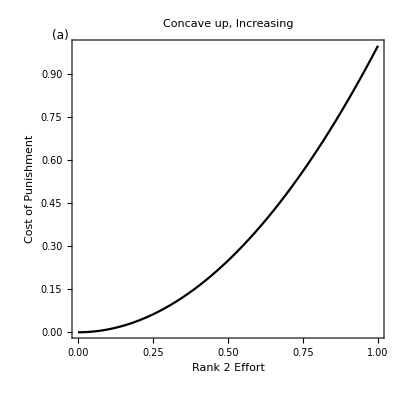

```mathematica
P2=Plot[{Concupinc[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},FrameLabel->{Style["Rank 2 Effort",12,FontFamily->Arial,FontColor->Black],Style["Cost of Punishment",12,FontFamily->Arial,FontColor->Black]},BaseStyle->{FontFamily->Arial,FontSize->8},Epilog->Text[Style["(a)",{Black,12}],Offset[{-20,5},Scaled[{0,1}]],{-1,0}],PlotRangeClipping->False,PlotLabel->"Concave up, Increasing",PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
```

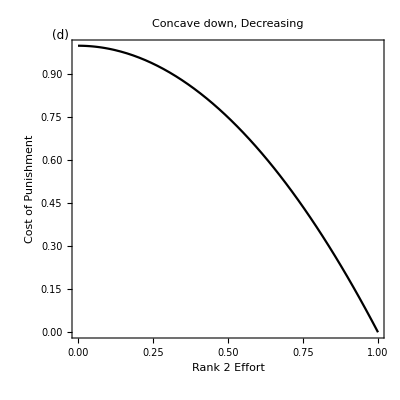

```mathematica
P3=Plot[{Concdowndec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->{"a)","b"},FrameTicks->None,Frame->{{True,False},{True,False}},Epilog->Text[Style["(d)",{Black,12}],Offset[{-20,5},Scaled[{0,1}]],{-1,0}],PlotRangeClipping->False,FrameLabel->{Style["Rank 2 Effort",12,FontFamily->Arial,FontColor->Black],Style["Cost of Punishment",12,FontFamily->Arial,FontColor->Black]},PlotLabel->"Concave down, Decreasing",BaseStyle->{FontFamily->Arial,FontSize->8},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
```

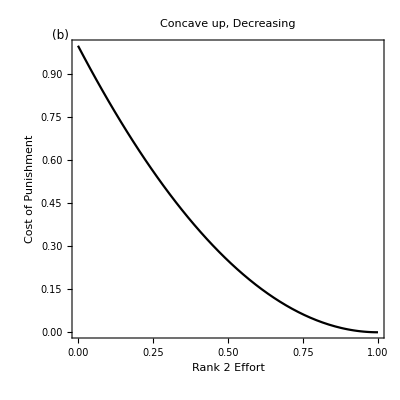

```mathematica
P4=Plot[{Concupdec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},FrameLabel->{Style["Rank 2 Effort",12,FontFamily->Arial,FontColor->Black],Style["Cost of Punishment",12,FontFamily->Arial,FontColor->Black]},
PlotLabel->"Concave up, Decreasing",BaseStyle->{FontFamily->Arial,FontSize->8},Epilog->Text[Style["(b)",{Black,12}],Offset[{-20,5},Scaled[{0,1}]],{-1,0}],PlotRangeClipping->False,
PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
```

Plot all four panels on a grid

```mathematica
plots={{P2,P4},{P1,P3}};
xlabels={"",Style["Kp'\n +",FontSize->12,FontFamily->Arial],Style["Kp'\n -",FontSize->12,FontFamily->Arial]};
ylabels={Style["Kp''\n +",FontSize->12,FontFamily->Arial],Style["Kp''\n -",FontSize->12,FontFamily->Arial]};
Grid[Join[{xlabels},Transpose[Join[{ylabels},Transpose[plots]]]],Frame->{None,None,{{2,2}->True,{2,3}->True,{3,2}->True,{3,3}->True}},Spacings->{2,1}]
```

| Kp'
 + | Kp'
 -
Kp''
 + | -Graphics- | -Graphics-
Kp''
 - | -Graphics- | -Graphics-

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure1highres.pdf",Out[232],ImageResolution->1200]
plot1=Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure1highres.pdf"]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Figure1highres.pdf

{-Graphics-}

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure1highres.svg",plot1,ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Figure1highres.svg

```mathematica
plot1=Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure1highres.pdf"]
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure1highres.tif",plot1,ImageResolution->1200]
```

{-Graphics-}

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure1highres.tif

Figure 2 - Change in Rank 1 fitness for different shapes of cost and benefit functions

Clear all previous functions

```mathematica
ClearAll[W1diff,u1,u2,ustar,Bprime,Bdprime,Kcprime,Kcdprime,Kp,lambda2,lambda1]
```

Let W1diff be the Taylor expanded rank 1 fitness - the fitness of rank 1 at ESS in the original model

```mathematica
W1diff[u1_,u2_,ustar_,Bprime_,Bdprime_,Kcprime_,Kcdprime_,Kp_]:=(u1+u2-2*ustar)*Bprime+0.5(u1+u2-2*ustar)^2*Bdprime-(u1-ustar)Kcprime+0.5(u1-ustar)^2*Kcdprime-Kp
```

The final negotiated level of effort of rank 1, u1, is found by differentiating the fitness of rank 1 wrt u1 and solving for u1:

```mathematica
u1[ustar_,Kcdprime_,Kpoprime_,lambda2_,Kpdprime_,Kpprime_,Bdprime_,Kpprime_,Kpodprime_]:=ustar+(Kcdprime*Kpoprime*lambda2 + Kpdprime*Kpoprime*lambda2-Kpodprime*Kpprime*lambda2+Bdprime(Kpprime(-1+lambda2)+Kpoprime(-1+lambda1)*lambda2))/(Kcdprime(Kcdprime+Kpdprime)+Bdprime*(Kpdprime*(-1+lambda2)+Kpodprime*(-1+lambda1)*lambda2+Kcdprime(-2+lambda1+lambda2)))
```

Analagously, we find the final negotiated level of effort of rank 2, u2 by solving W2diff for u2:

```mathematica
u2[ustar_,Kcdprime_,Kpoprime_,lambda2_,Kpdprime_,Kpprime_,Bdprime_,Kpprime_,Kpodprime_]:=ustar+(-Kcdprime*Kpprime+Bdprime(Kpprime-Kpprime*lambda2+Kpoprime(1-lambda2)lambda2))/(Kcdprime(Kcdprime+Kpdprime)+Bdprime*(Kpdprime*(-1+lambda2)+Kpodprime*(-1+lambda1)*lambda2+Kcdprime(-2+lambda1+lambda2)))
```

Let lambda 1 be the negative slope of the rank 1 response rule and lambda 2 be the negative slope of the rank 2 response rule

```mathematica
lambda2[lambda1_,Bdprime_,Kcdprime_,Kpdprime_,Kpodprime_]:=(1-lambda1)*Bdprime/(Kcdprime+Kpdprime-(1-lambda1)Bdprime)
lambda1[lambda2_,Bdprime_,Kcdprime_,Kpdprime_,Kpodprime_]:=((1-lambda2)Bdprime+Kpodprime)/(Kcdprime-(1-lambda2)Bdprime)
```

Sub in lambda 1 into lambda 2 to solve the two equations simultaneously:

```mathematica
((1-lambda2)Bdprime+Kpodprime)/(Kcdprime-(1-lambda2)Bdprime)/.lambda2->(1-lambda1)*Bdprime/(Kcdprime+Kpdprime-(1-lambda1)Bdprime)
(1-lambda1)*Bdprime/(Kcdprime+Kpdprime-(1-lambda1)Bdprime)/.lambda1->((1-lambda2)Bdprime+Kpodprime)/(Kcdprime-(1-lambda2)Bdprime)
```

(Kpodprime+Bdprime (1-(Bdprime (1-lambda1))/(Kcdprime+Kpdprime-Bdprime (1-lambda1))))/(Kcdprime-Bdprime (1-(Bdprime (1-lambda1))/(Kcdprime+Kpdprime-Bdprime (1-lambda1))))

(Bdprime (1-(Kpodprime+Bdprime (1-lambda2))/(Kcdprime-Bdprime (1-lambda2))))/(Kcdprime+Kpdprime-Bdprime (1-(Kpodprime+Bdprime (1-lambda2))/(Kcdprime-Bdprime (1-lambda2))))

Solve for lambda 1:

```mathematica
Simplify[Solve[(Kpodprime+Bdprime (1-(Bdprime (1-lambda1))/(Kcdprime+Kpdprime-Bdprime (1-lambda1))))/(Kcdprime-Bdprime (1-(Bdprime (1-lambda1))/(Kcdprime+Kpdprime-Bdprime (1-lambda1))))==lambda1,lambda1]]
```

{{lambda1→-((2 Bdprime Kcdprime-Kcdprime^2+Bdprime Kpdprime-Kcdprime Kpdprime+Bdprime Kpodprime+√(-4 Bdprime (2 Bdprime-Kcdprime) (-2 Bdprime^2+Bdprime (Kcdprime+Kpdprime-Kpodprime)+(Kcdprime+Kpdprime) Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)-Bdprime (2 Kcdprime+Kpdprime+Kpodprime))^2))/(2 Bdprime (2 Bdprime-Kcdprime)))},{lambda1→(-2 Bdprime Kcdprime+Kcdprime^2-Bdprime Kpdprime+Kcdprime Kpdprime-Bdprime Kpodprime+√(-4 Bdprime (2 Bdprime-Kcdprime) (-2 Bdprime^2+Bdprime (Kcdprime+Kpdprime-Kpodprime)+(Kcdprime+Kpdprime) Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)-Bdprime (2 Kcdprime+Kpdprime+Kpodprime))^2))/(2 Bdprime (2 Bdprime-Kcdprime))}}

Solve for lambda 2

```mathematica
Simplify[Solve[(Bdprime (1-(Kpodprime+Bdprime (1-lambda2))/(Kcdprime-Bdprime (1-lambda2))))/(Kcdprime+Kpdprime-Bdprime (1-(Kpodprime+Bdprime (1-lambda2))/(Kcdprime-Bdprime (1-lambda2))))==lambda2,lambda2]]
```

{{lambda2→-((-2 Bdprime Kcdprime+Kcdprime^2-Bdprime Kpdprime+Kcdprime Kpdprime+Bdprime Kpodprime+√(-4 Bdprime^2 (-2 Bdprime+Kcdprime+Kpdprime) (2 Bdprime-Kcdprime+Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)+Bdprime (-2 Kcdprime-Kpdprime+Kpodprime))^2))/(2 Bdprime (-2 Bdprime+Kcdprime+Kpdprime)))},{lambda2→-((-2 Bdprime Kcdprime+Kcdprime^2-Bdprime Kpdprime+Kcdprime Kpdprime+Bdprime Kpodprime-√(-4 Bdprime^2 (-2 Bdprime+Kcdprime+Kpdprime) (2 Bdprime-Kcdprime+Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)+Bdprime (-2 Kcdprime-Kpdprime+Kpodprime))^2))/(2 Bdprime (-2 Bdprime+Kcdprime+Kpdprime)))}}

Sub into the change in rank1 fitness the solutions for lambda1 and lambda2 at ESS, and choose realistic values for cost and benefit parameters:

```mathematica
Wdiffnocost[Kpprime_,Kpdprime_]:=(u1+u2-2ustar)*Bprime+0.5(u1+u2-2ustar)^2*Bdprime-(u1-ustar)Kcprime-0.5(u1-ustar)^2*Kcdprime/.u1->ustar+(Kcdprime*Kpoprime*lambda2 + Kpdprime*Kpoprime*lambda2-Kpodprime*Kpprime*lambda2+Bdprime(Kpprime(-1+lambda2)+Kpoprime(-1+lambda1)*lambda2))/(Kcdprime(Kcdprime+Kpdprime)+Bdprime*(Kpdprime*(-1+lambda2)+Kpodprime*(-1+lambda1)*lambda2+Kcdprime(-2+lambda1+lambda2)))/.u2->ustar+(-Kcdprime*Kpprime+Bdprime(Kpprime-Kpprime*lambda2+Kpoprime(1-lambda2)lambda2))/(Kcdprime(Kcdprime+Kpdprime)+Bdprime*(Kpdprime*(-1+lambda2)+Kpodprime*(-1+lambda1)*lambda2+Kcdprime(-2+lambda1+lambda2)))/.lambda1->((2 Bdprime Kcdprime-Kcdprime^2+Bdprime Kpdprime-Kcdprime Kpdprime+Bdprime Kpodprime+√(-4 Bdprime (2 Bdprime-Kcdprime) (-2 Bdprime^2+Bdprime (Kcdprime+Kpdprime-Kpodprime)+(Kcdprime+Kpdprime) Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)-Bdprime (2 Kcdprime+Kpdprime+Kpodprime))^2))/(2 Bdprime (2 Bdprime-Kcdprime)))/.lambda2->((-2 Bdprime Kcdprime+Kcdprime^2-Bdprime Kpdprime+Kcdprime Kpdprime+Bdprime Kpodprime-√(-4 Bdprime^2 (-2 Bdprime+Kcdprime+Kpdprime) (2 Bdprime-Kcdprime+Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)+Bdprime (-2 Kcdprime-Kpdprime+Kpodprime))^2))/(2 Bdprime (-2 Bdprime+Kcdprime+Kpdprime)))/.Kcdprime->1/.Kpoprime->0/.Kpodprime->0/.Bprime->1/.Bdprime->-.5/.Kcprime->1
```

Plot the concave up and concave down decreasing functions:

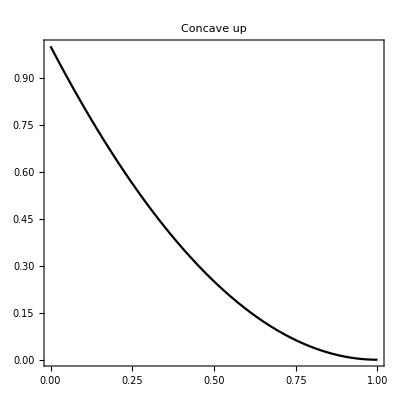

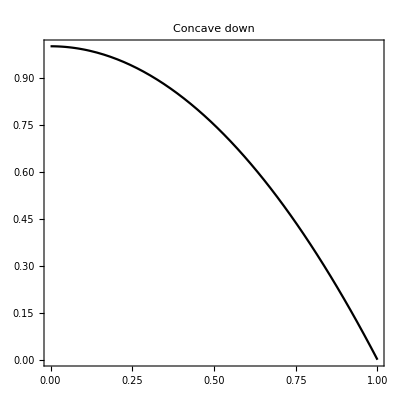

```mathematica
concup=Plot[{Concupdec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},PlotLabel->Style["Concave up",FontColor->Black,FontSize->10],BaseStyle->{FontFamily->Arial},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
concdown=Plot[{Concdowndec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},PlotLabel->Style["Concave down",FontColor->Black,FontSize->10],BaseStyle->{FontFamily->Arial},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
```

Plot the change in rank 1 fitness, relative to the original negotiation model:

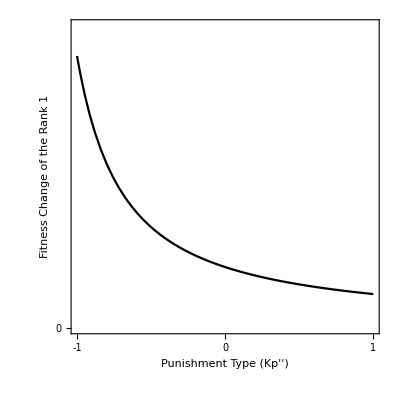

```mathematica
Plot[Wdiffnocost[Kpprime,Kpdprime]/.Kpprime->-0.1,{Kpdprime,-1,1},PlotRange-> {{-1,1},{0,0.4}},BaseStyle->{FontFamily->Arial},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,FrameTicks->{{-1,0,1},{0,1}},FrameLabel-> {Style["Punishment Type (Kp'')",16,FontFamily->Arial,FontColor->Black],Style["Fitness Change of the Rank 1",16,FontFamily->Arial,FontColor->Black]},AxesStyle->{{Dashed,Opacity[0]},{Dashed,Opacity[1]}},AspectRatio->1,PlotRangeClipping->False,ImagePadding->{{All,All},{100,All}},Epilog->{Inset[concup,{.8,-.05},Automatic,Scaled[.2]],Inset[concdown,{-.69,-.05},Automatic,Scaled[.2]]}]
```

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure2highres.pdf",Out[117],ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Figure2highres.pdf

```mathematica
plot2=Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure2highres.pdf"]
```

{-Graphics-}

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure2highres.svg",plot2,ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure2highres.svg

```mathematica
plot3=Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure3highres.pdf"]
```

{-Graphics-}

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure2highres.svg",plot2,ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure2highres.svg

Figure 3 - Effect of negotiation on response rules of rank 1 and rank 2

Define the fitness functions for rank 1 and rank 2 as the benefit - cost

```mathematica
B1[u1c_,u2c_]:=2(u1c+u2c)-(u1c+u2c)^2
K1[u1c_,u1p_]:=k1c*u1c^2+k1p*u1p^2
B2[u1c_,u2c_]:=2(u1c+u2c)-(u1c+u2c)^2
K2[u2c_,u1p_]:=k2c*u2c^2+k2p*u1p^2
```

u1p is assumed to be some function of u2c, that maximizes rank 1 fitness

```mathematica
W1[u1c_,u2c_,u1p_,k1c_,k1p_]:=2(u1c+u2c)-(u1c+u2c)^2-(k1c*u1c^2+k1p*u2c^2)
W2[u1c_,u2c_,u1p_,k2c_,k2p_]:=2(u1c+u2c)-(u1c+u2c)^2-(k2c*u2c^2+k2p*u2c^2)
```

Replace u1c with the response rule of rank 1 and find the optimal level of effort for rank 2 given responsiveness lambda1 of rank 1

```mathematica
W2a:=W2[u1c,u2c,u1p,k2c,k2p]/.u1c->r1hat[u2c]
```

```mathematica
D[W2a,u2c]
```

-2 k2c u2c-2 k2p u2c+2 (1+r1hat'[u2c])-2 (u2c+r1hat[u2c]) (1+r1hat'[u2c])

```mathematica
Solve[-2 k2c u2c-2 k2p u2c+2 (1-lambda1)-2 (u2c+u1c) (1-lambda1)==0,u2c]
```

{{u2c→(1-lambda1-u1c+lambda1 u1c)/(1+k2c+k2p-lambda1)}}

Analagous to above, replace u1c with the response rule of rank 2 and find the optimal level of effort for rank 1 given responsiveness lambda1 of rank 1

```mathematica
W1a:=W1[u1c,u2c,u1p,k1c,k1p]/.u2c->r2hat[u1c]
```

```mathematica
Solve[D[W1a,u1c]==0/.r2hat[u1c]->u2c/.r2hat'[u1c]->-lambda2,u1c]
```

{{u1c→(1-lambda2-u2c+lambda2 u2c+k1p lambda2 u2c)/(1+k1c-lambda2)}}

```mathematica
u1Nrule[u2c_,k1c_,k1p_,lambda2_]:=(1-lambda2-u2c+lambda2 u2c+k1p lambda2 u2c)/(1+k1c-lambda2)
u2Nrule[u1c_,k2c_,k2p_,lambda1_]:=(1-lambda1-u1c+lambda1 u1c)/(1+k2c+k2p-lambda1)
```

Find the negotiated levels of effort by solving the above two equations simultaneously:

```mathematica
Solve[u1Nrule[u2c,k1c,k1p,lambda2]==u1c,u2c]
```

{{u2c→(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+u1c)/(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+(k1p lambda2)/(1+k1c-lambda2))}}

```mathematica
Simplify[(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+u1c)/(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+(k1p lambda2)/(1+k1c-lambda2))]
```

(-1+lambda2+u1c+k1c u1c-lambda2 u1c)/(-1+lambda2+k1p lambda2)

```mathematica
Simplify[Solve[u2Nrule[u1c,k2c,k2p,lambda1]==u2c,u1c]]
```

{{u1c→(-1+lambda1+(1+k2c+k2p) u2c-lambda1 u2c)/(-1+lambda1)}}

```mathematica
Simplify[Solve[(1-lambda2-u2c+lambda2 u2c+k1p lambda2 u2c)/(1+k1c-lambda2)==(-1+lambda1+(1+k2c+k2p) u2c-lambda1 u2c)/(-1+lambda1),u2c]]
Simplify[Solve[(-1+lambda2+u1c+k1c u1c-lambda2 u1c)/(-1+lambda2+k1p lambda2)==(1-lambda1-u1c+lambda1 u1c)/(1+k2c+k2p-lambda1),u1c]]
```

{{u2c→(k1c (-1+lambda1))/(-k2p-k1c (1+k2c+k2p-lambda1)+k2c (-1+lambda2)-k1p lambda2+k2p lambda2+k1p lambda1 lambda2)}}

{{u1c→(k2c+k2p-k2c lambda2-k2p lambda2-k1p (-1+lambda1) lambda2)/(k2c+k2p+k1c (1+k2c+k2p-lambda1)+k1p lambda2-k2c lambda2-k2p lambda2-k1p lambda1 lambda2)}}

```mathematica
u2star:=(k1c (-1+lambda1))/(-k2p-k1c (1+k2c+k2p-lambda1)+k2c (-1+lambda2)-k1p lambda2+k2p lambda2+k1p lambda1 lambda2)
u1star:=(k2c+k2p-k2c lambda2-k2p lambda2-k1p (-1+lambda1) lambda2)/(k2c+k2p+k1c (1+k2c+k2p-lambda1)+k1p lambda2-k2c lambda2-k2p lambda2-k1p lambda1 lambda2)
```

These are the negotiated levels of effort for rank 1 and rank 2

```mathematica
u1Nrule[u2c_,k1c_,k1p_,lambda2_]:=(1-lambda2-u2c+lambda2 u2c+k1p lambda2 u2c)/(1+k1c-lambda2)
u2Nrule[u1c_,k2c_,k2p_,lambda1_]:=(1-lambda1-u1c+lambda1 u1c)/(1+k2c+k2p-lambda1)
u2Nrulea[u2c_,k1c_,k1p_,lambda1_]:=(1-lambda1-u2c+lambda1 u2c)/(1+k1c+k1p-lambda1)
```

I set lambda 1 as the negative slope of the response rule of rank 1 and lambda 2 as the negative slope of the response rule of rank 2, so we can solve for lambda 1 and lambda 2 in terms of the cost function parameters k1c, k2c, k1p, and k2p.

```mathematica
D[u1Nrule[u2c,k1c,k1p,lambda2],u2c]
```

(-1+lambda2+k1p lambda2)/(1+k1c-lambda2)

```mathematica
D[u2Nrule[u1c,k2c,k2p,lambda1],u1c]
```

(-1+lambda1)/(1+k2c+k2p-lambda1)

Assume k1c=k2c

```mathematica
Solve[lambda2==(-1+lambda1)/(1+k1c+k2p-lambda1),lambda1]
```

{{lambda1→(1+lambda2+k1c lambda2+k2p lambda2)/(1+lambda2)}}

```mathematica
Eliminate[{lambda2==(-1+lambda1)/(1+k1c+k2p-lambda1)&&lambda1==(-1+lambda2+k1p lambda2)/(1+k1c-lambda2)},lambda2]
Simplify[Solve[k1p lambda2 (1+lambda2)==2+k1c+k1c lambda2+k1c lambda2+k1c k1c lambda2+k2p lambda2+k1c k2p lambda2-2 lambda2^2-k1c lambda2^2-k2p lambda2^2,lambda2]]
```

k1p (-1+lambda1)==2+k1c+k2p+2 k1c lambda1+k1c^2 lambda1+k2p lambda1+k1c k2p lambda1-2 lambda1^2-k1c lambda1^2&&1+k1c+k2p-lambda1≠0

{{lambda2→(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/(2 (2+k1c+k1p+k2p))},{lambda2→(2 k1c+k1c^2-k1p+k2p+k1c k2p+√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/(2 (2+k1c+k1p+k2p))}}

```mathematica
Simplify[Solve[k1p (-1+lambda1)==2+k1c+k2p+2 k1c lambda1+k1c^2 lambda1+k2p lambda1+k1c k2p lambda1-2 lambda1^2-k1c lambda1^2,lambda1]]
```

{{lambda1→(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/(2 (2+k1c))},{lambda1→(2 k1c+k1c^2-k1p+k2p+k1c k2p+√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/(2 (2+k1c))}}

Assuming lambda1 and lambda 2 are between 0 and 1, then here lambda 2 is greater than lambda 1 (because the denominator is smaller for lambda 2 than lambda 1 if k1p and k2p are negative)

Find the McNamara et al. negotiation rule by setting k1c=k2c and k1p=k2p=0 (symmetric costs of caring and no punishment cost)

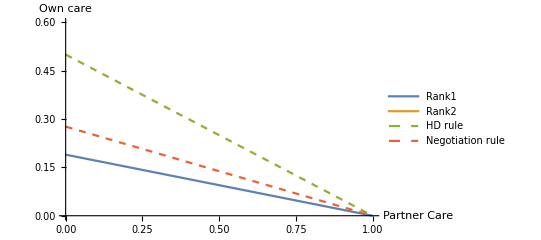

```mathematica
Plot[{u1Nrule[u2c,k1c,k1p,lambda2]/.lambda2->-1/(2 (2+k1c+k1p+k2p))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->1/.k1p->0/.k2p->-.5,u2N[u2c,k2c,k2p,lambda1]/.k2c->k1c/.lambda1->-1/(2 (2+k1c))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->1/.k1p->0/.k2p->-.5,(1-u2c)/(1+k1c)/.k1c->1/.k1p->0/.k2p->-.5,(1+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c))-u2c-((2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2)) u2c)/(2 (2+k1c)))/(1+k1c+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c)))/.k1c->1/.k1p->0/.k2p->-.5},{u2c,0,1},PlotRange->{{0,1},{0,.6}},PlotLegends->{"Rank1","Rank2","HD rule","Negotiation rule"},PlotStyle->{Default,Default,Dashed,Dashed},AxesLabel->{"Partner Care","Own care"},AspectRatio->Automatic]
```

Above shows a plot with k1c=1, k1p=0, and k2p=-0.5

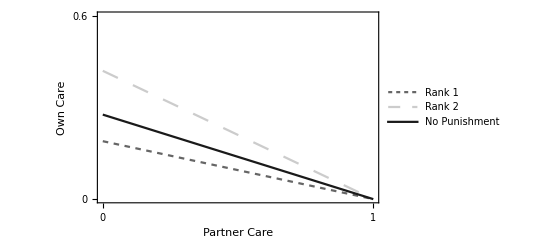

```mathematica
Plot[{u1Nrule[u2c,k1c,k1p,lambda2]/.lambda2->-1/(2 (2+k1c+k1p+k2p))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->1/.k1p->0/.k2p->-.5,u2Nrule[u2c,k2c,k2p,lambda1]/.k2c->k1c/.lambda1->-1/(2 (2+k1c))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->1/.k1p->0/.k2p->-.5,(1+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c))-u2c-((2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2)) u2c)/(2 (2+k1c)))/(1+k1c+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c)))/.k1c->1},{u2c,0,1},PlotRange->{{0,1},{0,.6}},BaseStyle->{FontFamily->Arial},PlotLegends->Placed[{"Rank 1","Rank 2","No Punishment"},{0.78,0.8}],PlotStyle->{{Dashing[{0.01}],GrayLevel[.4]},{Dashing[{.03}],GrayLevel[.8]},GrayLevel[.1],"Dashed","Dashed","Automatic"},Frame-> {True,True,False,False},FrameStyle->Black,FrameTicks->{{0,1},{0,.6}},FrameLabel-> {Style["Partner Care",16,FontFamily->Arial,FontColor->Black],Style["Own Care",16,FontFamily->Arial,FontColor->Black]},AspectRatio->Automatic]
```

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure3highres.pdf",Out[148],ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Figure3highres.pdf

```mathematica
plot3 = Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Figure3highres.pdf",ImageResolution->1200]
```

{-Graphics-}

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure3svg.svg",Out[248],ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure3svg.svg

```mathematica
u1Nrule[u2c,k1c,k1p,lambda2]/.lambda2->-1/(2 (2+k1c+k1p+k2p))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1p->0/.k2p->0
```

(1+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c))-u2c-((2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2)) u2c)/(2 (2+k1c)))/(1+k1c+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c)))

A numeric solution for lambda 1 and lambda 2. For some values of k1c, k2p, and k1p lambda 1 and 2 are between 0 and 1 (biparental care is ESS) and lambda 2 is greater than lambda 1 (rank 2 is more responsive than rank 1)

```mathematica
NSolve[lambda1==-1/(2 (2+k1c))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->2/.k2p->-1/.k1p->-.5]
```

{{lambda1→0.360191}}

```mathematica
NSolve[lambda2==-1/(2 (2+k1c+k1p+k2p))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->2/.k2p->-1/.k1p->-.5,lambda2]
```

{{lambda2→0.576305}}

Figure 4

Next I will create a response rule plot, with u2c on the x axis and u1c on the y axis. Where the lines intersect is the ES negotiated level of care.

```mathematica
u1Nrule[u2c_,k1c_,k1p_,lambda2_]:=(1-lambda2-u2c+lambda2 u2c+k1p lambda2 u2c)/(1+k1c-lambda2)
u2Nrule[u1c_,k1c_,k2p_,lambda1_]:=(1-lambda1-u1c+lambda1 u1c)/(1+k1c+k2p-lambda1)
```

```mathematica
Simplify[Solve[u1Nrule[u2c,k1c,k1p,lambda2]==0,u2c]]
Simplify[Solve[u2Nrule[u1c,k1c,k2p,lambda1]==0,u1c]]
```

{{u2c→(-1+lambda2)/(-1+lambda2+k1p lambda2)}}

{{u1c→1}}

```mathematica
Solve[u2c==(1-lambda1-u1c+lambda1 u1c)/(1+k1c+k2p-lambda1),u1c]
```

{{u1c→(1/(1+k1c+k2p-lambda1)-lambda1/(1+k1c+k2p-lambda1)-u2c)/(1/(1+k1c+k2p-lambda1)-lambda1/(1+k1c+k2p-lambda1))}}

```mathematica
u2N[u2c_,k1c_,k2p_,lambda1_]:=(1/(1+k1c+k2p-lambda1)-lambda1/(1+k1c+k2p-lambda1)-u2c)/(1/(1+k1c+k2p-lambda1)-lambda1/(1+k1c+k2p-lambda1))
```

```mathematica
u1N[k1c_,lambda2_,u2c_,k1p_]:=(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+u2c)/(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+(k1p lambda2)/(1+k1c-lambda2))
```

```mathematica
Solve[(1-lambda2-u2c+lambda2 u2c+k1p lambda2 u2c)/(1+k1c-lambda2)==u1c,u2c]
```

{{u2c→(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+u1c)/(-1/(1+k1c-lambda2)+lambda2/(1+k1c-lambda2)+(k1p lambda2)/(1+k1c-lambda2))}}

Install package for plotting stars:

```mathematica
(*Load the package code*)package=Import["http://raw.github.com/AlexeyPopkov/PolygonPlotMarkers/master/PolygonPlotMarkers.m","Text"];

(*Install the package (existing file will be overwritten!)*)
Export[FileNameJoin[{$UserBaseDirectory,"Applications","PolygonPlotMarkers.m"}],package,"Text"];
```

Below I just rearranged things so that the rank 2 is on the y axis and set values for k1p, k2p, and k1c assuming no cost to rank 1 of punishing rank 2.

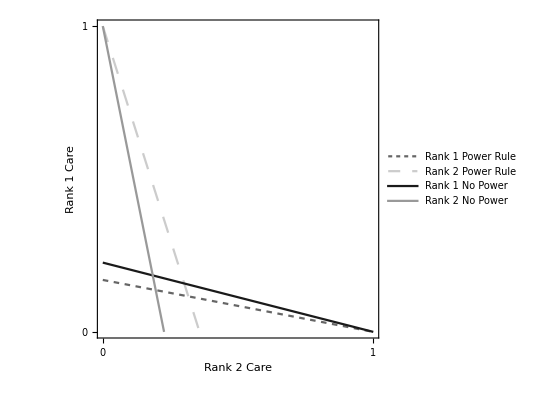

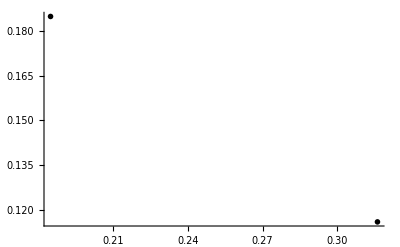

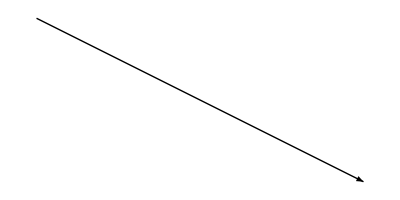

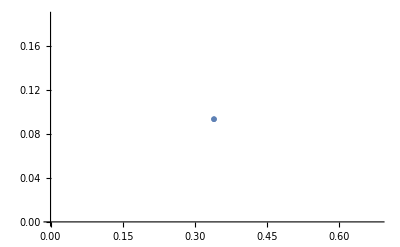

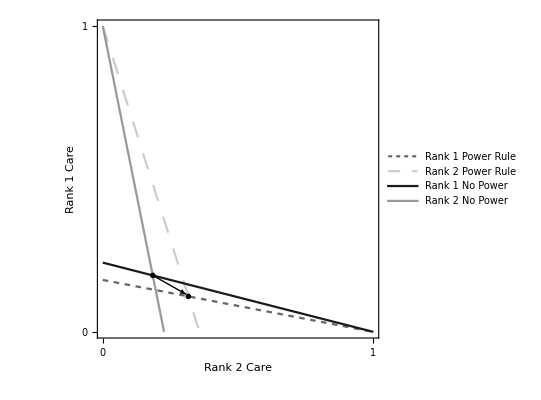

```mathematica
P=Plot[{u1Nrule[u2c,k1c,k1p,lambda2]/.lambda2->-1/(2 (2+k1c+k1p+k2p))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->2/.k1p->0/.k2p->-1,u2N[u2c,k1c,k2p,lambda1]/.lambda1->-1/(2 (2+k1c))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->2/.k1p->0/.k2p->-1,(1+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c))-u2c-((2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2)) u2c)/(2 (2+k1c)))/(1+k1c+(2 k1c+k1c^2-√(4 (2+k1c)^2+(2 k1c+k1c^2)^2))/(2 (2+k1c)))/.k1c->2,(-(-4+√((2+k1c)^2 (4+k1c^2))) (-1+u2c)+k1c^2 (-1+3 u2c)+k1c (-4+8 u2c))/(-4-4 k1c-k1c^2+√((2+k1c)^2 (4+k1c^2)))/.k1c->2},{u2c,0,1},PlotRange->{{0,1},{0,1}},BaseStyle->{FontFamily->Arial},PlotLegends->Placed[{"Rank 1 Power Rule","Rank 2 Power Rule","Rank 1 No Power","Rank 2 No Power"},{0.7,0.8}],PlotStyle->{{Dashing[{0.01}],GrayLevel[.4]},{Dashing[{.03}],GrayLevel[.8]},GrayLevel[.1],GrayLevel[0.6]},Frame-> {True,True,False,False},FrameStyle->Black,FrameTicks->{{0,1},{0,1}},FrameLabel-> {Style["Rank 2 Care",16,FontFamily->Arial,FontColor->Black],Style["Rank 1 Care",16,FontFamily->Arial,FontColor->Black]},AspectRatio->Automatic]
G=ListPlot[{{0.31617773616313855,0.11617773616313866},{0.18469903125906462,0.18469903125906462}},PlotMarkers->{"✶",15},PlotStyle->Black]
V=Graphics[{Arrow[{{0.1847,0.1847},{0.308,0.123}}]}]
F=ListPlot[{{0.3396,0.09332}},PlotMarkers->{Graphics[{Black,Star[{0,0}]}],0.1}]
Show[P,G,V]
```

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure4pdf.pdf",Out[166],ImageResolution->1200]
plot4 = Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure4pdf.pdf",ImageResolution->1200]
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure4svg.svg",plot4,ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure4pdf.pdf

{-Graphics-}

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure4svg.svg

```mathematica
P
```

-Graphics-

We can solve for the final negotiated level of effort for given parameter values, and the solution is shown with a * on the plot above

```mathematica
u1Nrule[u2c,k1c,k1p,lambda2]/.lambda2->-1/(2 (2+k1c+k1p+k2p))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->2/.k1p->0/.k2p->-1
```

(1+1/6 (5-√73)-u2c-1/6 (5-√73) u2c)/(3+1/6 (5-√73))

```mathematica
u2N[u2c,k1c,k2p,lambda1]/.lambda1->-1/(2 (2+k1c))(2 k1c+k1c^2-k1p+k2p+k1c k2p-√(4 (2+k1c) (2+k1c+k1p+k2p)+(k1c^2-k1p+k2p+k1c (2+k2p))^2))/.k1c->2/.k1p->0/.k2p->-1
```

(1/(2+1/8 (5-√73))+(5-√73)/(8 (2+1/8 (5-√73)))-u2c)/(1/(2+1/8 (5-√73))+(5-√73)/(8 (2+1/8 (5-√73))))

```mathematica
NSolve[(1+1/6 (5-√73)-u2c-1/6 (5-√73) u2c)/(3+1/6 (5-√73))==(1/(2+1/8 (5-√73))+(5-√73)/(8 (2+1/8 (5-√73)))-u2c)/(1/(2+1/8 (5-√73))+(5-√73)/(8 (2+1/8 (5-√73)))),u2c]
```

{{u2c→0.316178}}

```mathematica
(1/(2+1/8 (5-√73))+(5-√73)/(8 (2+1/8 (5-√73)))-u2c)/(1/(2+1/8 (5-√73))+(5-√73)/(8 (2+1/8 (5-√73))))/.u2c->0.31617773616313855
```

0.116178

Above is the final negotiated level of effort when there is punishment. Next, we solve for the same parameter values but in the original negotiation model

```mathematica
NSolve[(1+1/8 (8-8 √2)-u2c-1/8 (8-8 √2) u2c)/(3+1/8 (8-8 √2))==((4-8 √2) (-1+u2c)+4 (-1+3 u2c)+2 (-4+8 u2c))/(-16+8 √2),u2c]
```

{{u2c→0.184699}}

```mathematica
(1+1/8 (8-8 √2)-u2c-1/8 (8-8 √2) u2c)/(3+1/8 (8-8 √2))/.u2c->0.184699
```

0.184699

Figure 5 - Do offspring do better with punishment?

We can find the total effort by adding the effort of rank 1 and rank 2 at the ESS and plotting it as a function of Kp’’

```mathematica
utot[Kpprime_,Kpdprime_]:=(Kcdprime*Kpoprime*lambda2 + Kpdprime*Kpoprime*lambda2-Kpodprime*Kpprime*lambda2+Bdprime(Kpprime(-1+lambda2)+Kpoprime(-1+lambda1)*lambda2))/(Kcdprime(Kcdprime+Kpdprime)+Bdprime*(Kpdprime*(-1+lambda2)+Kpodprime*(-1+lambda1)*lambda2+Kcdprime(-2+lambda1+lambda2)))+(-Kcdprime*Kpprime+Bdprime(Kpprime-Kpprime*lambda2+Kpoprime(1-lambda2)lambda2))/(Kcdprime(Kcdprime+Kpdprime)+Bdprime*(Kpdprime*(-1+lambda2)+Kpodprime*(-1+lambda1)*lambda2+Kcdprime(-2+lambda1+lambda2)))/.lambda1->((2 Bdprime Kcdprime-Kcdprime^2+Bdprime Kpdprime-Kcdprime Kpdprime+Bdprime Kpodprime+√(-4 Bdprime (2 Bdprime-Kcdprime) (-2 Bdprime^2+Bdprime (Kcdprime+Kpdprime-Kpodprime)+(Kcdprime+Kpdprime) Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)-Bdprime (2 Kcdprime+Kpdprime+Kpodprime))^2))/(2 Bdprime (2 Bdprime-Kcdprime)))/.lambda2->((-2 Bdprime Kcdprime+Kcdprime^2-Bdprime Kpdprime+Kcdprime Kpdprime+Bdprime Kpodprime-√(-4 Bdprime^2 (-2 Bdprime+Kcdprime+Kpdprime) (2 Bdprime-Kcdprime+Kpodprime)+(Kcdprime (Kcdprime+Kpdprime)+Bdprime (-2 Kcdprime-Kpdprime+Kpodprime))^2))/(2 Bdprime (-2 Bdprime+Kcdprime+Kpdprime)))/.Kcdprime->1/.Kpoprime->0.5*Kpprime/.Kpodprime->0.5*Kpdprime/.Bprime->1/.Bdprime->-.5/.Kcprime->1
```

```mathematica
concup=Plot[{Concupdec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},PlotLabel->Style["Concave up",FontColor->Black,FontSize->10],BaseStyle->{FontFamily->Arial},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
concdown=Plot[{Concdowndec[u2c]},{u2c,0,1},PlotRange->{{0,1},{0,1}},FrameTicks->None,Frame->{{True,False},{True,False}},PlotLabel->Style["Concave down",FontColor->Black,FontSize->10],BaseStyle->{FontFamily->Arial},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,AspectRatio->Automatic]
```

-Graphics-

-Graphics-

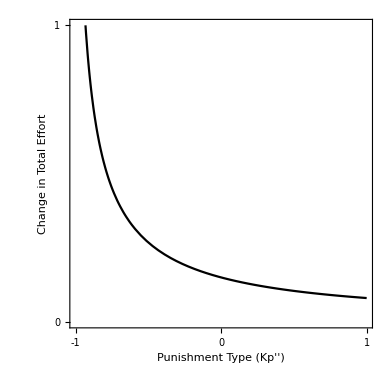

```mathematica
Plot[utot[Kpprime,Kpdprime]/.Kpprime->-.3,{Kpdprime,-1,1},PlotRange->{{-1,1},{0,1}},BaseStyle->{FontFamily->Arial},PlotStyle->{Black},Frame-> {True,True,False,False},FrameStyle->Black,FrameTicks->{{-1,0,1},{0,1}},FrameLabel-> {Style["Punishment Type (Kp'')",16,FontFamily->Arial,FontColor->Black],Style["Change in Total Effort",16,FontFamily->Arial,FontColor->Black]},AxesStyle->{{Dashed,Opacity[0]},{Dashed,Opacity[1]}},AspectRatio->1,PlotRangeClipping->False,ImagePadding->{{All,All},{90,All}},Epilog->{Inset[concup,{.8,-.13},Automatic,Scaled[.2]],Inset[concdown,{-.7,-.13},Automatic,Scaled[.2]]}]
```

```mathematica
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure5pdf.pdf",Out[177],ImageResolution->1200]
plot5 = Import["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure5pdf.pdf",ImageResolution->1200]
Export["C:\\Users\\tbarb\\Documents\\Spring_2019\\Power Model\\Final_documents\\Accepted\\Figure5svg.svg",plot5,ImageResolution->1200]
```

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure5pdf.pdf

{-Graphics-}

C:\Users\tbarb\Documents\Spring_2019\Power Model\Final_documents\Accepted\Figure5svg.svg